Evaluating this notebook generates a plot for the nullclines for the system in Project 1 part b.

The first command clears everything from previous evaluations, and then we create the matrix with the given parameters.

```mathematica
Clear["Global`*"]
```

```mathematica
A={{0.21,0.13},{0.1,0.08}}
```

{{0.21,0.13},{0.1,0.08}}

```mathematica
k=5
```

5

Now we set up the system given in terms of the coefficient matrix A.

```mathematica
f1=A[[1,1]]*x1-A[[1,2]]*x2*x1
f2=-A[[2,1]]*x2  + A[[2,2]]*x2*x1
```

0.21 x1-0.13 x1 x2

-0.1 x2+0.08 x1 x2

We can create a plot of vector arrows similar to a slope field by using the StreamPlot command, specifying the functions as inputs and inputting the ranges.

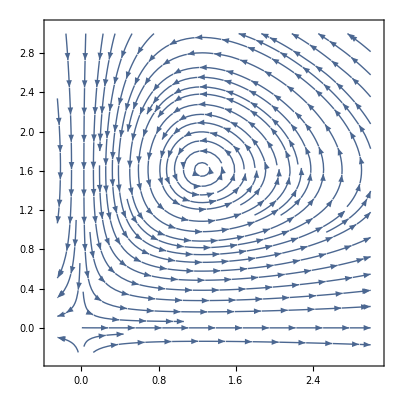

```mathematica
vecplot = StreamPlot[{f1,f2},{x1,-0.25,3},{x2,-0.25,3},Axes->True]
```

We can generate the nullclines as a separate plot using the four equations obtained from solving the equilibria of the system by hand.

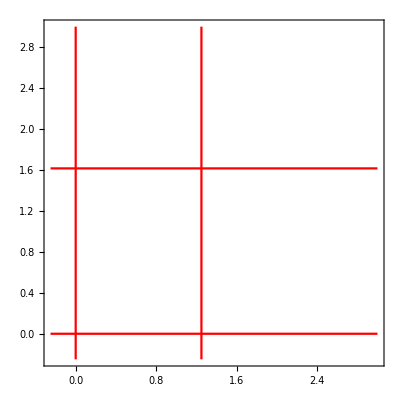

```mathematica
nullclines=ContourPlot[{x==0,y==0,x==0.1/0.08,y==0.21/0.13},{x,-0.25,3},{y,-0.25,3},ContourStyle->{Red}]
```

Finally we can overlay the two plots to show a plot of circulation about the nullclines.

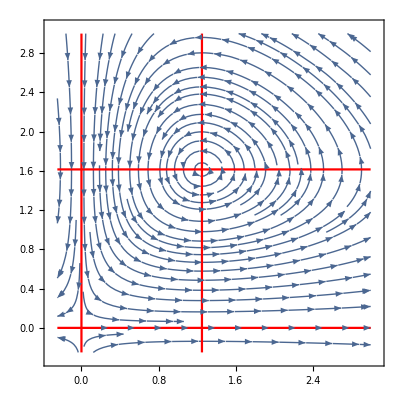

```mathematica
Show[vecplot,nullclines]
```